```mathematica
DSolve[y''[x] == -y'[x]^2 + 2*g*k*x*y'[x]+4*b*T*g, y[x], x] // Simplify
```

{{y[x]→C[2]+-((4 b √g T C[1] HermiteH[-1-(2 b T)/k,√g √k K[1]])/(√k)-4 b g T Hypergeometric1F1[1+(b T)/k,3/2,g k K[1]^2] K[1])/(C[1] HermiteH[-(2 b T)/k,√g √k K[1]]+Hypergeometric1F1[(b T)/k,1/2,g k K[1]^2])K[1]1x}}

```mathematica
HermiteH[-1-2T, 0]
```

(2^(-1-2 T) √π)/Gamma[1/2 (2+2 T)]

```mathematica
HermiteH[-2T,0]
```

(2^(-2 T) √π)/Gamma[1/2 (1+2 T)]

```mathematica
Hypergeometric1F1[T,1/2,0]
```

1

```mathematica
InverseLaplaceTransform[(HermiteH[-2T,0]+1)^-1]
```

```mathematica
InverseLaplaceTransform[1/(r+a), r, t]
```

ⅇ^(-3 (-1+e) t)

```mathematica
pr[t_] :=InverseLaplaceTransform[-c*kb*kon/((s+c*kb)*(s+kon)), s, t]
```

```mathematica
pr[t]
```

(c (ⅇ^(-c kb t)-ⅇ^(-kon t)) kb kon)/(c kb-kon)

```mathematica
f[c_] := Evaluate[Log[pr[t]]]
f[c]
```

Log[(c (ⅇ^(-c kb t)-ⅇ^(-kon t)) kb kon)/(c kb-kon)]

```mathematica
g[t_]:=FullSimplify[f''[c]]
```

```mathematica
g[t]
```

-1/c^2+kb^2 (1/(-c kb+kon)^2-(ⅇ^((c kb+kon) t) t^2)/((ⅇ^(c kb t)-ⅇ^(kon t))^2))

```mathematica
exp :=FullSimplify[Integrate[-kb^2*t^2*E^(-c*kb*t)/(1-E^(-(kon-c*kb)*t))^2, t]]
exp2 := exp -1/c^2 - kb^2/(kon-c*kb)^2
```

```mathematica
With[{c=5.6, kb=0.0888,kon=5, ku=5, koff=5, dc=0.56, t=0.001}, Evaluate[exp2]]
```

0.0963554

```mathematica
With[{c=5.6, kb=0.0888,kon=5, ku=5, koff=5, dc=0.56, t=0.001}, Evaluate[2/c^2]]
```

0.0637755

```mathematica
(1/(c*kb)+1/kon+1/ku+1/koff)*(-1/c^2+kb^2/(kon-c*kb)^2-2*kon/(c^2*kb^2*(kon-c*kb)))
```

```mathematica
exp:=(-1/c^2+kb^2/(-c kb+kon)^2-(2 kon)/(c^2 kb^2 (-c kb+kon))) *(1/(1/(c*kb)+1/kon+1/ku+1/koff))*(-(dc)^2/2)
```

```mathematica
With[{c=5.6, kb=0.0888,kon=5, ku=5, koff=5, dc=0.56}, Evaluate[exp]]
```

0.541244

```mathematica
exp2 := (1/2)*(dc/c)^2*(c*kb)
```

```mathematica
With[{c=5.6, kb=0.0888,kon=5, ku=5, koff=5, dc=0.56}, Evaluate[exp2]]
```

0.0024864

```mathematica
f[x_, mu_, sig_]:=(e^((x-mu)^2 / (2*sig^2)))/Sqrt[2*Pi*sig^2]
```

```mathematica
Evaluate[f[x, mu, sig]]
```

(e^((-mu+x)^2/(2 sig^2)))/(√(2 π) √(sig^2))

```mathematica
Integrate[f[x, mu, sig]^2, {x, -Infinity, Infinity}]
```

ConditionalExpression[1/(2 √π sig^2 √(-Log[e]/sig^2)), Re[Log[e]/sig^2]<0]

```mathematica
FullSimplify[%]
```

ConditionalExpression[1/(√2 √(sig^2) √(-Log[e]/sig^2)), Re[Log[e]/sig^2]<0]

```mathematica
f[x_, mu_, sig_]:=(e^(-(x-mu)^2 / (2*sig^2)))/Sqrt[2*Pi*sig^2]
```

```mathematica
Evaluate[f[dx, V*dt, Sqrt[2*V*dt]]]
```

(e^(-(dx-dt V)^2/(4 dt V)))/(2 √π √(dt V))

```mathematica
g[V_] :=f[dx, V*dt, Sqrt[2*V*dt]]
```

```mathematica
Evaluate[g'[V]]
```

-(dt e^(-(dx-dt V)^2/(4 dt V)))/(4 √π (dt V)^(3/2))+(e^(-(dx-dt V)^2/(4 dt V)) ((dx-dt V)/(2 V)+(dx-dt V)^2/(4 dt V^2)) Log[e])/(2 √π √(dt V))

```mathematica
Factor[%]
```

-(e^(-(dx-dt V)^2/(4 dt V)) (2 dt V-dx^2 Log[e]+dt^2 V^2 Log[e]))/(8 √π V (dt V)^(3/2))

```mathematica
Simplify[%]
```

(dt e^(-(dx-dt V)^2/(4 dt V)) (-2 dt V+(dx^2-dt^2 V^2) Log[e]))/(8 √π (dt V)^(5/2))

```mathematica
%/g[V]
```

(-2 dt V+(dx^2-dt^2 V^2) Log[e])/(4 dt V^2)

```mathematica
Solve[%==0, V]
```

{{V→(-dt-√(dt^2+dt^2 dx^2 Log[e]^2))/(dt^2 Log[e])},{V→(-dt+√(dt^2+dt^2 dx^2 Log[e]^2))/(dt^2 Log[e])}}

```mathematica
FullSimplify[%]
```

{{V→-(dt+√(dt^2 (1+dx^2 Log[e]^2)))/(dt^2 Log[e])},{V→(-dt+√(dt^2 (1+dx^2 Log[e]^2)))/(dt^2 Log[e])}}

General::munfl: Exp[-490506.] is too small to represent as a normalized machine number; precision may be lost.

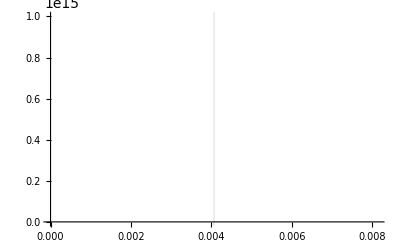

```mathematica
k' = 40;
dt' = 1;
dXs = RandomVariate[NormalDistribution[0.01,0.1], k'];
mu = Mean[dXs];
var = Mean[dXs^2];
P := ((4*Pi*V*dt)^(-k/2))*Exp[-Total[(dXs - V*dt)^2]/(4*V*dt)];
Vest = (-1+Sqrt[1+dXs[[1]]^2])/dt';
Vestk = (-1+ Sqrt[1 + var])/dt';
Plot[With[{V=x, dt=dt', k=k'}, Evaluate[P]], {x, 0, 2*Vestk}, GridLines->{{Vestk,0}}]
```